# Name | M# |

## Exam Tuesday

## Models

Population models https://en.wikipedia.org/wiki/Population_model

Growth of population p'=(birth rate - death rate)p
Estimate death rate using life expectancy and birth rate using litter size etc.

Predator (wolf w) prey (moose m) https://en.wikipedia.org/wiki/Lotka%E2%80%93Volterra_equations
m' | = |    α m | - | β m w
w' | = | -γ w | + | δ m w

Earth-Moon probe M=1/82.45, E=1-M, r_1=√((x+M)^2+y^2) and r_2=√((x-E)^2+y^2) 
	x'' | = |    2y' | + | x | - | (E(x+M))/r_1^3 | - | (M(x-E))/r_2^3
y'' | = | -2x' | + | y | - | (E y)/r_1^3 | - | (M y)/r_2^3

Mixing in Tanks y'=A y+f    with y(0)=y_0 volume v and salt s

v'(t) = rate in - rate out and s'(t) = rate in - rate out

```mathematica
A={{-7/100.0,5/200,0},{7/100,-9/200,2/700},{0,4/200,-4/700}};
f={6,0,0};y0={100,200,2100}; TMax=5000;
ySol=NDSolveValue[{y'[t]==A.y[t]+f,y[0]==y0},y,{t,0, TMax}];
TabView[{
"v_i vs t"->Plot[ySol[t],{t,0, TMax},PlotRange->All,AxesLabel->{"t","v_i"}],
"v_1 vs v_2 vs v_3"->ParametricPlot3D[ySol[t],{t,0, TMax},PlotRange->All,AxesLabel->{"v_1","v_2","v_3"},PlotLabel->Eigenvalues[A]]}]
```

12

RLC circuits https://en.wikipedia.org/wiki/RLC_circuit
-Graphics-ODE
V+q' R + q'' L+q/C = 0                  
q is charge on the capacitor          
 I=i=q' is the current                          
Figure from wiki page above.        
R,L,and C are constants                 
As y'=A y+f system d/dt(q
i)=(0 | 1
-1/RC | -1/LR)(q
i)+(0
-V/L)

```mathematica
{v,r,l,c}={9,1.0,10,10}; TMax=100;
A ={{0,1},{-1/(r c), -1/(r l)}};f={0,-v/l};y0={0,0}; 
ySol=NDSolveValue[{y'[t]==A.y[t]+f,y[0]==y0},y,{t,0, TMax}];
TabView[{
"i & q vs t"->Plot[ySol[t],{t,0, TMax},PlotRange->All,AxesLabel->{"t","i & q"}],
"i vs q"->ParametricPlot[ySol[t],{t,0, TMax},PlotRange->All,AxesLabel->{"q","i"},PlotLabel->Eigenvalues[A]]}]
```

12

## Linear Algebra Review

We are going to learn how to write down the general solution of 
	y'=A y 
from the eigenvalues and eigenvectors of the matrix A.

Just a reminder

A v_i=λ_i v_i  with ||v_i||≠0 defines an eigenvalue λ_i and associated eigenvector v_i.

Eigenvalues and eigenvectors can be complex.

Almost all n×n matrices have an eigenvector basis {v_1,v_2,…,v_n}.  V=[v_1|v_2|…|v_n] gives V^-1.A.V=diag(λ_1,λ_2,…,λ_n).  This is diagonalization.

```mathematica
n=4;
A=RandomReal[{-1,1},{n,n}];
{λs,V}=Eigensystem[A];V=Vᵀ;
λs
MatrixForm[Inverse[V].A.V]
```

{-0.900268,0.774685,-0.12763,0.0371144}

(-0.900268 | -8.88178×10^-16 | 5.55112×10^-16 | -5.55112×10^-16
-2.22045×10^-16 | 0.774685 | -1.38778×10^-16 | 1.66533×10^-16
-6.73073×10^-16 | 2.7929×10^-16 | -0.12763 | 3.81639×10^-17
-7.42462×10^-16 | 2.08167×10^-16 | 8.32667×10^-17 | 0.0371144)

## Linear Algebra Review and ODE y'=A y

Suppose I have A v_1=λ_1 v_1 then y_1(t)=c_1 ⅇ^(λ_1 t)v_1 solves y'=A y.

All the eigen-pairs A v_i=λ_i v_i give solutions y_i(t)=c_i ⅇ^(λ_i t)v_i.

y'=A y is linear so y(t)=∑_(i=1)^n c_i ⅇ^(λ_i t)v_i is an n parameter family of solutions.

If the eigen-vectors are Linearly Independent (LI) then there are unique coefficients c=(c_1
c_2
⋮
c_n) satisfying y(0)=∑_(i=1)^n c_i ⅇ^(λ_i 0)v_i=y_0. All we do is solve  V c=y_0.

Summary.  The solution of y'=A y with y(0)=y_0 is y(t)=∑_(i=1)^n c_i ⅇ^(λ_i t)v_i with V c =[v_1|…|v_n]c=y_0

You can rewrite a second order ODE as a first order system.
L i'+R i+q/C+12=0 with i=q' is the same as
(q
i)'=(q'
-q/(C L)-i/(R L)-12)=(i
-q/(C L)-i/(R L)-12)=(0 | 1
-1/(C L) | -1/(R L))(q
i)+(0
-12)

We need to know how to think about complex eigenvalues λ=a±b ⅈ.

We need to know what e^(a + b ⅈ)=e^a e^(b ⅈ) means.

Starts of Series

e^t | = | 1+t+t^2/2+t^3/6+t^4/24+t^5/120+t^6/720+t^7/5040+t^8/40320+O[t]^9

sin(t) | = | t-t^3/6+t^5/120-t^7/5040+O[t]^9

cos(t) | = | 1-t^2/2+t^4/24-t^6/720+t^8/40320+O[t]^9

Full Series

e^t=∑_(n=0)^∞ 1/(n!)t^n

sin(t)=∑_(j=0)^∞ (-1)^j/((2j+1)!)t^(2j+1)

cos(t)=∑_(j=0)^∞ (-1)^j/((2j)!)t^(2j)

E^(b ⅈ)=∑_(n=0)^∞ 1/(n!)(b ⅈ)^n=1+ⅈ b-b^2/2-(ⅈ b^3)/6+b^4/24+(ⅈ b^5)/120-b^6/720-(ⅈ b^7)/5040+b^8/40320+O(b^9)

E^(b ⅈ)=(1-b^2/2+b^4/24-b^6/720+b^8/40320+…)+ⅈ (b-b^3/6+b^5/120-b^7/5040+…)

E^(b ⅈ)=cos(b)+ⅈ sin(b)

e^((a ± b ⅈ)t)=e^(a t)(cos(b t)±ⅈ sin(b t)).

Solutions grow or decay according to e^(a t)

Solutions wiggle like sin(bt) or cos(bt)

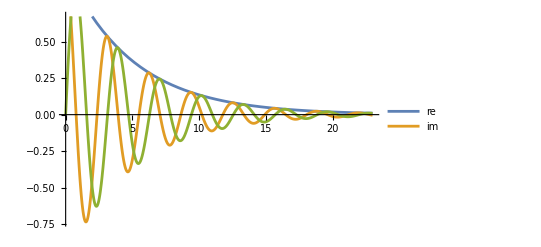

```mathematica
{a,b}={-0.2,2};
Plot[{E^(a t),Re[ⅇ^((a+b ⅈ)t)],Im[ⅇ^((a+b ⅈ)t)]},{t,0, 23},
PlotLegends->{"re","im"}]
```

```mathematica
A=({{-1., 6, 1}, {-6, -2, 1}, {1, 1, -5}});
Eigenvalues[A]
y0={7,4,5};TMax=3;
ySol=NDSolveValue[{y'[t]==A.y[t],y[0]==y0},y,{t, 0, TMax}];
TabView[{
"t-y"->Plot[ySol[t],{t,0, TMax},PlotRange->All],
"3D y"->ParametricPlot3D[ySol[t],{t,0, TMax},PlotRange->All]
}]
```

{-1.42563+5.85552 ⅈ,-1.42563-5.85552 ⅈ,-5.14874+0. ⅈ}

12

```mathematica
A={{-1,2,0},{2,-4,0},{0,0,0.1}};
Eigenvalues[A]
Eigenvectors[A]
```

{-5.,0.1,0.}

{{0.447214,-0.894427,0.},{0.,0.,1.},{0.894427,0.447214,0.}}